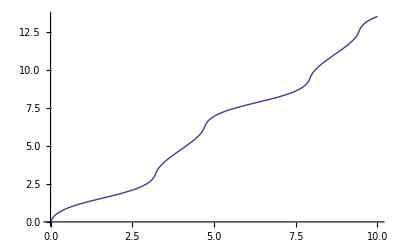

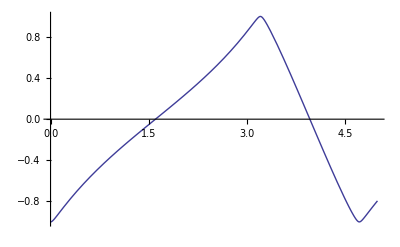

-Graphics-

```mathematica
Clear["Global`*"];
(* Q - parameters Q = (q1 == alpha) *)
(* Configuration *)
X := {-l*Cos[q1[t]], 0, 0 , l*Sin[q1[t]]}
dX = Simplify[D[X,t]];
m = ({{m1, 0, 0, 0}, {0, m1, 0, 0}, {0, 0, m2, 0}, {0, 0, 0, m2}});
(* Trig->False disabled trig. simplifications *)
T = Simplify[(m.dX.dX) / 2, Trig->False];
U = m2*g*(l*Sin[q1[t]]);

(* Lagrange *)
L = T - U;
dtdq1 = D[D[L,q1'[t]],t];
dq1 = D[L,q1[t]];

LangrageDiff = Simplify[dtdq1 - dq1];

(* Example *)
m1 = 20;
m2 = 1;
g = 9.81;
l = 1;
q1 = First[q1 /. NDSolve[{LangrageDiff == 0, q1[0] ==0, q1'[0] == 5},q1, {t,0,10}]];
Plot[{q1[t]}, {t,0,10}]

Plot[X[[1]], {t,0,5}]
Plot[-1*Cos[q1[t]], {t,0,5}]
(*
Animate[Graphics[{Line{-1.5,0}, {1.5,0}}], Line[{{0,-1.5}, {0, 1.5}}], Line[{}]
*)

(* Prints *)

Print["X"]
MatrixForm[X]

Print["dX"]
MatrixForm[dX]

Print["m"]
MatrixForm[m]

Print["T"]
MatrixForm[T]

Print["U"]
MatrixForm[U]

Print["L"]
MatrixForm[L]

Print["dtdq1"]
MatrixForm[dtdq1]

Print["dq1"]
MatrixForm[dq1]

Print["LangrageDiff"]
MatrixForm[LangrageDiff]
```